```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,475,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>".dat"],{i,1,Length[mub]}];
```

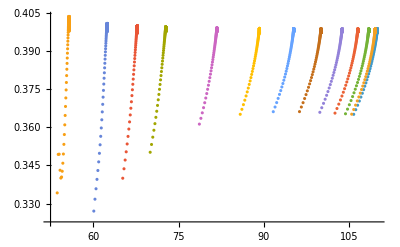

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T0p39=Table[Flatten[FindRoot[fitfun[[i]][x]-0.39==0,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p39.dat",%];
```

FindRoot::reged: 点 {89.2494} 位于搜索区域 {85.8579,89.2494} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {72.7655} 位于搜索区域 {70.0005,72.7655} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {67.7429} 位于搜索区域 {65.1686,67.7429} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{109.433,109.06,107.929,106.006,103.231,99.5118,94.7198,89.2494,81.258,72.7655,67.7429,62.4464,55.7494}

```mathematica
T0p38=Table[Flatten[FindRoot[fitfun[[i]][x]-0.38==0,{x,fitdata[[i]][[-3]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p38.dat",%];
```

FindRoot::reged: 点 {62.4464} 位于搜索区域 {60.0735,62.4464} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {55.7494} 位于搜索区域 {53.6309,55.7494} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

{108.346,107.974,106.845,104.928,102.164,98.4678,93.724,87.7965,80.5503,71.8949,67.0506,62.4464,55.7494}

```mathematica
T0p37=Table[Flatten[FindRoot[fitfun[[i]][x]-0.37==0,{x,fitdata[[i]][[50]][[1]],fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["beta0p37.dat",%];
```

FindRoot::reged: 点 {55.7494} 位于搜索区域 {53.6309,55.7494} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

{106.78,106.408,105.285,103.378,100.635,96.9819,92.3268,86.5774,79.6427,71.3774,66.6973,61.6664,55.7494}

```mathematica
Export["mub.dat",mub]
```

mub.dat

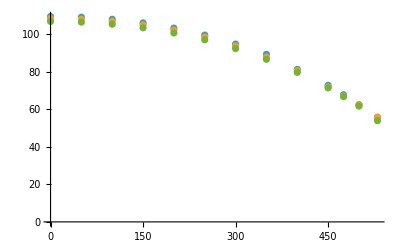

```mathematica
ListPlot[{Transpose[{mub,T0p39}],Transpose[{mub,T0p38}],Transpose[{mub,T0p37}]}]
```